# Superimposed Kerr Metric in Kerr-Schild coordinates.

## Import metric

```mathematica
Import["~/llgsks.mx"];
Import["~/uugsks.mx"];

llgSKS=(llgSKS//.Ω->Sqrt[(M1+M2)/b^3]);
uugSKS=(uugSKS//.Ω->Sqrt[(M1+M2)/b^3]);
```

## Plot definitions

```mathematica
ClearAll[M1,M2,a1,a2,b]
M1=1/2;
M2=1/2;
a1=95/100*M1;
a2=95/100*M2;
b=3;
```

## Plots

### Ergosphere

```mathematica
N[llgSKS⟦1,1⟧//.{t->0,z->0,y->0,x->-3}]
```

0.142473

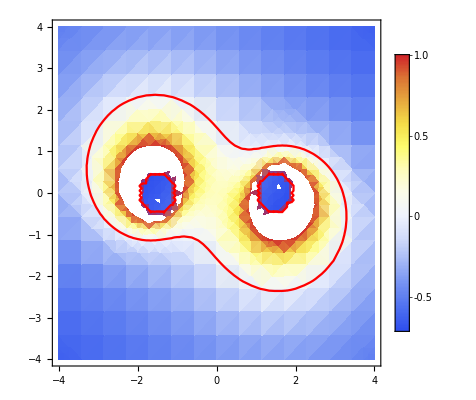

```mathematica
Show[
DensityPlot[
(llgSKS⟦1,1⟧)//.{t->0,z->0},
{x,-b-1,b+1},
{y,-b-1,b+1},

PlotPoints->15,
ColorFunction->"TemperatureMap",
PlotLegends->True,
PlotRange->{Full,Full,{-1,1}}
],

ContourPlot[
((llgSKS⟦1,1⟧)//.{t->0,z->0})==0,
{x,-b-1,b+1},
{y,-b-1,b+1},

PlotPoints->10,
ContourShading->None,
ContourStyle->Directive[Red,Thick],
PlotLegends->False,
PlotRange->{Full,Full,{-1,1}}
]
]
```

### Determinant

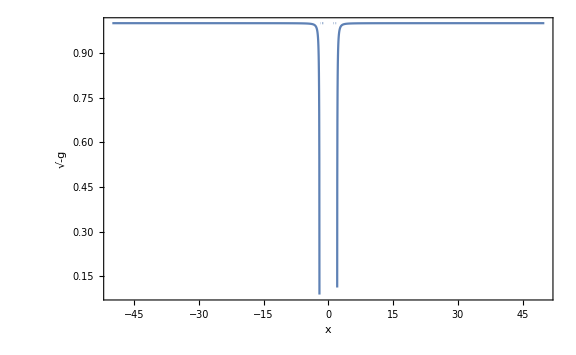

```mathematica
Plot[Sqrt[-Det[(llgSKS//.{t->0,y->0,z->0})]],{x,-50,50},PlotRange->Full,FrameLabel->{"x","√-g"},Axes->False,Frame->True,ImageSize->Large]
```

### Lower Shift

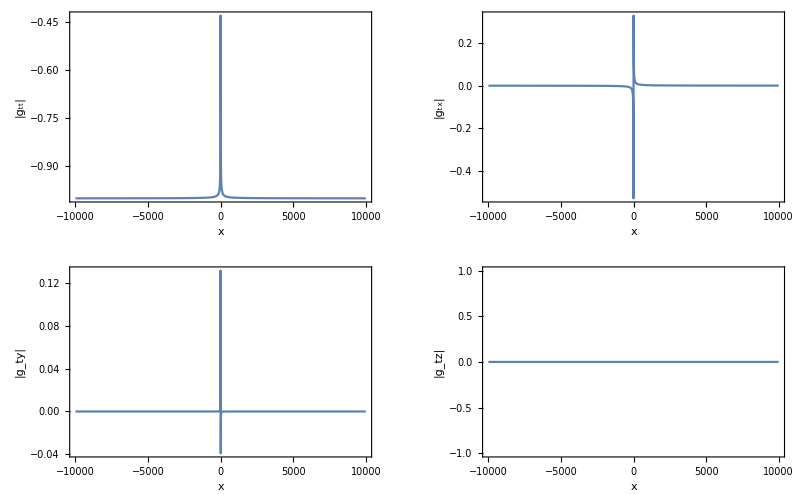

```mathematica
GraphicsGrid[
{
{
Plot[(llgSKS⟦1,1⟧//.{t->0,y->0,z->0}),{x,-10^4,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|g_tt|"},Axes->False,Frame->True,ImageSize->Large],
Plot[(llgSKS⟦1,2⟧//.{t->0,y->0,z->0}),{x,-10^4,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|g_tx|"},Axes->False,Frame->True,ImageSize->Large]
},
{
Plot[(llgSKS⟦1,3⟧//.{t->0,y->0,z->0}),{x,-10^4,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|g_ty|"},Axes->False,Frame->True,ImageSize->Large],
Plot[(llgSKS⟦1,4⟧//.{t->0,y->0,z->0}),{x,-10^4,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|g_tz|"},Axes->False,Frame->True,ImageSize->Large]
}
},
ImageSize->Full
]
```

### lower spatial metric

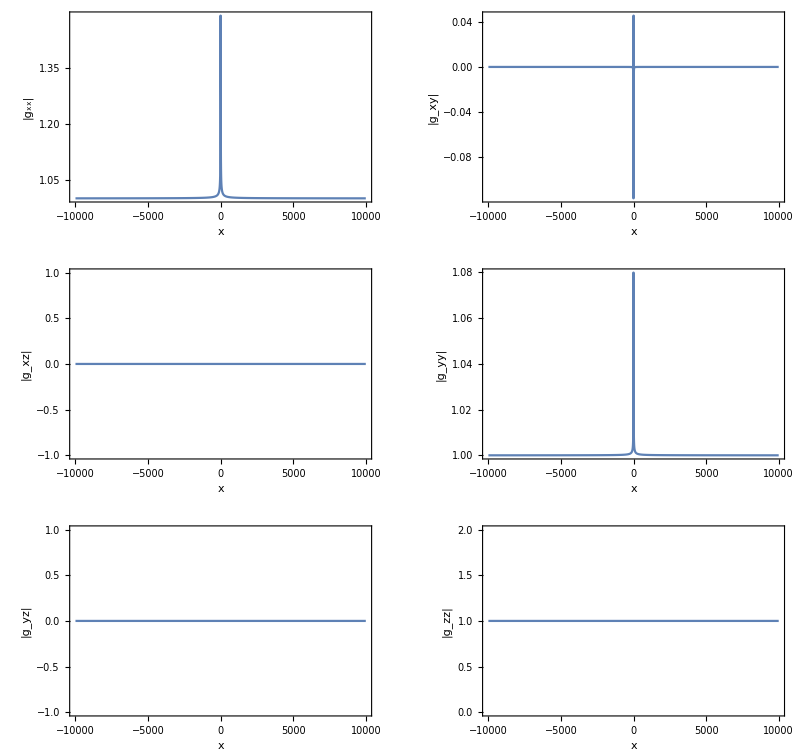

```mathematica
GraphicsGrid[
{
{
Plot[(llgSKS⟦2,2⟧//.{t->0,y->0,z->0}),{x,-10^4,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|g_xx|"},Axes->False,Frame->True,ImageSize->Large],
Plot[(llgSKS⟦2,3⟧//.{t->0,y->0,z->0}),{x,-10^4,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|g_xy|"},Axes->False,Frame->True,ImageSize->Large]
},
{
Plot[(llgSKS⟦2,4⟧//.{t->0,y->0,z->0}),{x,-10^4,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|g_xz|"},Axes->False,Frame->True,ImageSize->Large],
Plot[(llgSKS⟦3,3⟧//.{t->0,y->0,z->0}),{x,-10^4,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|g_yy|"},Axes->False,Frame->True,ImageSize->Large]
},
{
Plot[(llgSKS⟦3,4⟧//.{t->0,y->0,z->0}),{x,-10^4,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|g_yz|"},Axes->False,Frame->True,ImageSize->Large],
Plot[(llgSKS⟦4,4⟧//.{t->0,y->0,z->0}),{x,-10^4,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|g_zz|"},Axes->False,Frame->True,ImageSize->Large]
}
},
ImageSize->Full
]
```

### lapse

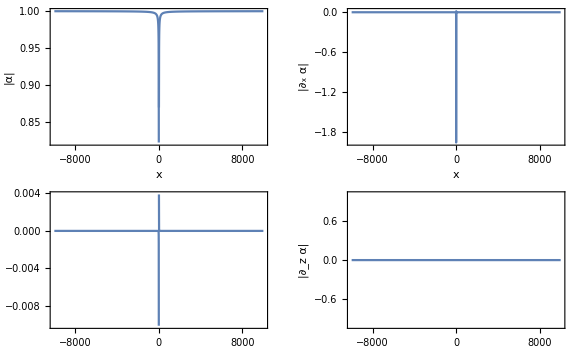

```mathematica
ClearAll[expr,expr1,expr2,expr3];
expr=√(1/-uugSKS⟦1,1⟧)//.{t->0,y->0,z->0};
expr1=D[√(1/-uugSKS⟦1,1⟧),x]//.{t->0,y->0,z->0};
expr2=D[√(1/-uugSKS⟦1,1⟧),y]//.{t->0,y->0,z->0};
expr3=D[√(1/-uugSKS⟦1,1⟧),z]//.{t->0,y->0,z->0};

GraphicsGrid[
{
{
Plot[expr,{x,-10^4,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|α|"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr1,{x,-10^4,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|∂_x α|"},Axes->False,Frame->True,ImageSize->Large]
},
{
Plot[expr2,{x,-10^4,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|∂_y α|"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr3,{x,-10^4,10^4},PlotRange->{Full,Full},FrameLabel->{"x","|∂_z α|"},Axes->False,Frame->True,ImageSize->Large]
}
},
ImageSize->Large
]
ClearAll[expr,expr1,expr2,expr3];
```